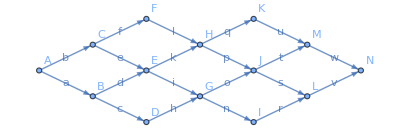

```mathematica
cpaGraph = EdgeTaggedGraph[{
"A" -> "B", "A" -> "C",
"B" -> "D", "B" -> "E",
"C" -> "E", "C" -> "F",
"D" -> "G",
"E" -> "G", "E" -> "H",
"F" -> "H",
"G" -> "I", "G" -> "J",
"H" -> "J", "H" -> "K",
"I" -> "L",
"J" -> "L", "J" -> "M",
"K" ->"M",
"L" -> "N",
"M" -> "N"
} -> {"a", "b", "c", "d", "e", "f", "h", "i", "k", "l", "n", "o", "p", "q", "r", "s", "t", "u", "v", "w"},
VertexLabels->"Name",
EdgeLabels->"EdgeTag", GraphLayout->{"SymmetricLayeredEmbedding", "Rotation"->90Degree}]
```

```mathematica
duration = <|
"A" -> 12,
"B" -> 10,
"C" -> 8,
"D" -> 9,
"E" -> 2,
"F" -> 11,
"G" -> 5,
"H" -> 14,
"I" -> 7,
"J" -> 6,
"K" -> 1,
"L" -> 13,
"M" -> 3,
"N" -> 4|>
```

<|A→12,B→10,C→8,D→9,E→2,F→11,G→5,H→14,I→7,J→6,K→1,L→13,M→3,N→4|>

```mathematica
Successors[g_, v_] := VertexOutComponent[g, {v}, {1}]
Predecessors[g_, v_] := VertexInComponent[g, {v}, {1}]
```

```mathematica
Clear[esRec, efRec]
efRec[v_] := efRec[v] = esRec[v] + duration[v]
esRec[v_] := esRec[v] = 
If[
Predecessors[cpaGraph, v] === {}, 0,
Max[efRec[#] &/@Predecessors[cpaGraph, v]]]
```

```mathematica
es = AssociationMap[esRec, VertexList[cpaGraph]]
ef = AssociationMap[efRec, VertexList[cpaGraph]]
```

<|A→0,B→12,C→12,D→22,E→22,F→20,G→31,H→31,I→36,J→45,K→45,L→51,M→51,N→64|>

```mathematica
<|"A"->12,"B"->22,"C"->20,"D"->31,"E"->24,"F"->31,"G"->36,"H"->45,"I"->43,"J"->51,"K"->46,"L"->64,"M"->54,"N"->68|>
```

```mathematica
latestFinish = ef["N"]
```

68

```mathematica
Clear[lsRec, lfRec]
lsRec[v_] := lsRec[v] = lfRec[v] - duration[v]
lfRec[v_] := lfRec[v] = 
If[
Successors[cpaGraph, v] === {}, latestFinish,
Min[lsRec[#] &/@Successors[cpaGraph, v]]]
```

```mathematica
ls = AssociationMap[lsRec, VertexList[cpaGraph]]
lf = AssociationMap[lfRec, VertexList[cpaGraph]]
```

<|A→0,B→19,C→12,D→30,E→29,F→20,G→39,H→31,I→44,J→45,K→60,L→51,M→61,N→64|>

<|A→12,B→29,C→20,D→39,E→31,F→31,G→44,H→45,I→51,J→51,K→61,L→64,M→64,N→68|>

```mathematica
float = ls - es
```

<|A→0,B→7,C→0,D→8,E→7,F→0,G→8,H→0,I→8,J→0,K→15,L→0,M→10,N→0|>

{A,C,F,H,J,L,N}

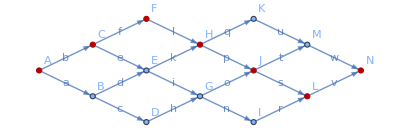

```mathematica
zeroFloat = Select[Normal[float], Last[#] === 0 &] // Map[First]
HighlightGraph[cpaGraph, zeroFloat]
```

```mathematica
es
ls
float
```

<|A→0,B→12,C→12,D→22,E→22,F→20,G→31,H→31,I→36,J→45,K→45,L→51,M→51,N→64|>

<|A→0,B→19,C→12,D→30,E→29,F→20,G→39,H→31,I→44,J→45,K→60,L→51,M→61,N→64|>

<|A→0,B→7,C→0,D→8,E→7,F→0,G→8,H→0,I→8,J→0,K→15,L→0,M→10,N→0|>